Here I will quickly calculate everything we need for the Sagnac 1550 source (actually, we now want to have a 1560 source!!!)

```mathematica
Print["Loading some useful constants using Windows file paths."];
<<"gaussdefs";
```

Loading some useful constants using Windows file paths.

```mathematica
NotebookEvaluate["gausspropagation.nb"]
```

NotebookEvaluate::nbnfnd: Unable to find the notebook gausspropagation.nb.

$Failed

### random stuff

```mathematica
unitV[θ_,ϕ_]:={Cos[ϕ] Sin[θ],Sin[ϕ] Sin[θ],Cos[θ]}
```

```mathematica
cmum=c 10^6;
```

```mathematica
ωtoλ[ω_]:=2 Pi cmum/ω
```

```mathematica
λtoω[λ_]:=2 Pi cmum/λ
```

```mathematica
c:=2.99792458 10^8;
```

### Definitions for LiNbO_3

the Sellmeier equations for the extraordinary index of refraction for LiNbO_3 are of the form (A,B,C,D,E, F are the Sellmeier coefficients, λ is the wavelength in μm). a is a list of 6 values, b is a list of 4 values (D. H. Jundt Opt. Lett. 22 (20), 1553 (1997), doi: 10.1364/OL.22.001553)

```mathematica
aJundt={5.35583,0.100473,0.20692,100,11.34927,1.5334 10^-2};
bJundt={4.629 10^-7,3.862 10^-8,-0.89 10^-8,2.657 10^-5};
f[T_,T0_]:=(T-T0) (T+T0+2 273.16)
```

here, fis “the square of the absolute temperature in degrees Kelvin, with an added offset to make it vanish at the reference temperature T0=24.5 °C” (D. H. Jundt (1997)). T is given in degree Celsius.

general form of Sellmeier equation:

```mathematica
nS[a_,b_,T_,λ_]:=Module[{f0,T0},
T0=24.5;
f0=f[T,T0];
Sqrt[a[[1]]+b[[1]] f0+(a[[2]]+b[[2]] f0)/(λ^2-(a[[3]]+b[[3]] f0)^2)+(a[[4]]+b[[4]] f0)/(λ^2-a[[5]]^2)-a[[6]] λ^2]
]
```

```mathematica
neJundt[T_,λ_]:=nS[aJundt,bJundt,T,λ]
```

```mathematica
neJundt[T_,λ_]:=nS[aJundt,bJundt,T,λ]
```

```mathematica
aN5eGayer={5.756,0.0983,0.2020,189.32,12.52,1.32 10^-2};
bN5eGayer={2.86 10^-6,4.7 10^-8,6.113 10^-8,1.516 10^-4};

aN5oGayer={5.653,0.1185,0.2091,89.61,10.85,1.97 10^-2};
bN5oGayer={7.941 10^-7,3.134 10^-8,-4.641 10^-9,-2.188 10^-6};

aN1eGayer={5.078,0.0964,0.2065,61.16,10.55,1.59 10^-2};
bN1eGayer={6.677 10^-7,7.822 10^-8,-2.653 10^-8,1.096 10^-4};
```

```mathematica
n5eGayer[T_,λ_]:=nS[aN5eGayer,bN5eGayer,T,λ]
```

```mathematica
n5oGayer[T_,λ_]:=nS[aN5oGayer,bN5oGayer,T,λ]
```

```mathematica
n1eGayer[T_,λ_]:=nS[aN1eGayer,bN1eGayer,T,λ]
```

now let's define a function calculating the refractive index in the direction given by a unit vector n:

```mathematica
getN5gayer[n_,λ_]:=Module[{nx,ny,nz},
nz=n5eGayer[λ];
nx=n5oGayer[λ];
ny=n5oGayer[λ];
(nx ny nz)/(√(n[[1]]^2 ny^2 nz^2+n[[2]]^2 nx^2 nz^2+n[[3]]^2 nx^2 ny^2))
]
```

temp dependent:

```mathematica
getN5gayerTemp[n_,λ_,T_]:=Module[{nx,ny,nz},
nz=n5eGayer[T,λ];
nx=n5oGayer[T,λ];
ny=n5oGayer[T,λ];
(nx ny nz)/(√(n[[1]]^2 ny^2 nz^2+n[[2]]^2 nx^2 nz^2+n[[3]]^2 nx^2 ny^2))
]
```

now the same but in dependence on ω instead of λ:

```mathematica
getNo5gayer[n_,ω_]:=getN5gayer[n,ωtoλ[ω]]
```

```mathematica
getNo5gayerTemp[n_,ω_,T_]:=getN5gayerTemp[n,ωtoλ[ω],T]
```

and now the same but with individual components:

```mathematica
getNoc5gayer[c1_,c2_,c3_,ω_]:=Module[{nx,ny,nz,λ},
λ=ωtoλ[ω];
nz=n5eGayer[λ];
nx=n5oGayer[λ];
ny=n5oGayer[λ];
(nx ny nz)/(√(c1^2 ny^2 nz^2+c2^2 nx^2 nz^2+c3^2 nx^2 ny^2))
]
```

```mathematica
getNoc5gayerTemp[c1_,c2_,c3_,ω_,T_]:=Module[{nx,ny,nz,λ},
λ=ωtoλ[ω];
nz=n5eGayer[T,λ];
nx=n5oGayer[T,λ];
ny=n5oGayer[T,λ];
(nx ny nz)/(√(c1^2 ny^2 nz^2+c2^2 nx^2 nz^2+c3^2 nx^2 ny^2))
]
```

```mathematica
GVtemp5gayer[n_,λ_,T_]:=Module[{ω},
ω=λtoω[λ];
cmum/(getN5gayerTemp[n,λ,T]+Derivative[0,0,0,1,0][getNoc5gayerTemp][n[[1]],n[[2]],n[[3]],ω,T] ω)
]
```

taking into account the expansion coefficients for Lithium Niobate, the poling period will depend on the temperature. This formula and the numeric values of the contants α and β are from the paper by Jundt et al. Opt. Lett.  22(20), 1553 (1997)

```mathematica
ΛtempLiNbO3[Λ0_,T_]:=Module[{TR,α,β},
TR=25;
α=1.54 10^-5;
β=5.3 10^-9;
Λ0 (1 + α(T-TR) + β(T-TR)^2)
]
```

### Step 3: measuring the the phase matching temperature of the SPDC crystals, optimal alignment

We will use the 780 laser to produce 1560 nm SPDC photon pairs. In the first step, I will use all power and just direct it toward one signal photon detector. Later, we can also look at coincidences.

RED in this next plot is related to the 780 nm. I am just to lazy to change it

The biggest difference compared to the 1310 single pass SPDC I am currently trying to achive is that I will use the numbers proposed in the Alessandro Fedrizzi paper from 2018. There he states that for the pump beam, the Rayleigh lenght should follow:
1.8 ≤ζ_pump ≤2.6; ζ_pump = L/(z_(Rayleigh, p))
And the signal and idler should follow: 
ζ_(s,i, SPDC) = 3.2; ζ_(s,i, SPDC)  = L/(z_(Rayleigh, i,s))
All this is calculated INSIDE the crystal, so you need to take into account the refractive index.

```mathematica
Module[{λp,λs,λi,ωp,ωs,ωi,Lcrystal,T,ns,ni,np,zRayleighPUMP1,zRayleighPUMP2,waistPUMP1,waistPUMP2,zRayleighSIGNAL,waistSIGNAL},
Lcrystal = 5 10^-2; 
T=28;
np=n5oGayer;
ns=n5eGayer;
ni=n5oGayer;
λp=780 10^-9; ωp=(2 π c)/λp;
λs=1560 10^-9; ωs=(2 π c)/λs;
λi = λs;ωi=(2 π c)/λi;

zRayleighPUMP1 = Lcrystal/1.8; (*INSIDE crystal*)
waistPUMP1 =w0[zRayleighPUMP1,λp/np[T,ωtoλ[ωp]]] ;

zRayleighPUMP2 = Lcrystal/2.6;(*INSIDE crystal*)
waistPUMP2 =w0[zRayleighPUMP2,λp/np[T,ωtoλ[ωp]]] ;

zRayleighSIGNAL = Lcrystal/3.2;(*INSIDE crystal*)
waistSIGNAL =w0[zRayleighSIGNAL,λs/ns[T,ωtoλ[ωs]]] ;

Print["Optimal waist for pump beam (inside the crystal): ",waistPUMP2 10^6," μm - ",waistPUMP1 10^6," μm"];

Print["Optimal waist for signal beam (inside the crystal): ",waistSIGNAL 10^6," μm"]
]
```

Optimal waist for pump beam (inside the crystal): 46.0091 μm - 55.2961 μm

Optimal waist for signal beam (inside the crystal): 60.3369 μm

Comment! am i acknowledging the refractive index TWICE now? I is this the number I see when I plot the thing on my plots? I think it is. but do I then need to correct the plot again?

-----------
I now want to determine the optimal crystal size:

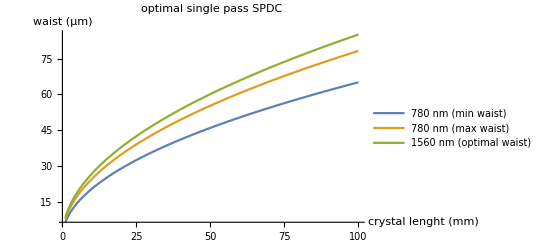

```mathematica
Module[{λp,λs,λi,ωp,ωs,ωi,Lcrystal,T,ns,ni,np,zRayleighPUMP1,zRayleighPUMP2,waistPUMP1,waistPUMP2,zRayleighSIGNAL,waistSIGNAL,Lcrystalmm},
Lcrystal = Lcrystalmm 10^-3; 
T=28;
np=n5oGayer;
ns=n5eGayer;
ni=n5oGayer;
λp=780 10^-9; ωp=(2 π c)/λp;
λs=1550 10^-9; ωs=(2 π c)/λs;
λi = λs;ωi=(2 π c)/λi;

zRayleighPUMP1 = Lcrystal/1.8; (*INSIDE crystal*)
waistPUMP1 =w0[zRayleighPUMP1,λp/np[T,ωtoλ[ωp]]] ;

zRayleighPUMP2 = Lcrystal/2.6;(*INSIDE crystal*)
waistPUMP2 =w0[zRayleighPUMP2,λp/np[T,ωtoλ[ωp]]] ;

zRayleighSIGNAL = Lcrystal/3.2;(*INSIDE crystal*)
waistSIGNAL =w0[zRayleighSIGNAL,λs/ns[T,ωtoλ[ωs]]] ;
Plot[{waistPUMP2 10^6,waistPUMP1 10^6,waistSIGNAL 10^6},{Lcrystalmm, 1,100},
PlotLegends->{" 780 nm (min waist)","780 nm (max waist)", " 1560 nm (optimal waist)"},
AxesLabel->{"crystal lenght (mm)","waist (μm)"},
PlotLabel->Style["optimal single pass SPDC"],
GridLines->{{},{0}}, PlotRange->All]
]
```

Now, knowing this this parameters i want to plot the waist of the beam at the crystal edge.

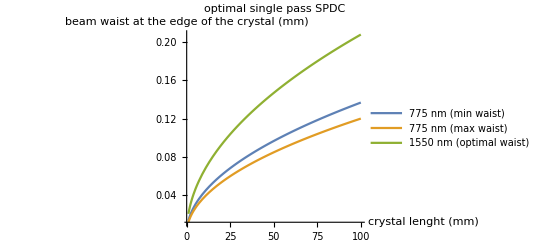

```mathematica
Module[{λp,λs,λi,ωp,ωs,ωi,Lcrystal,T,ns,ni,np,zRayleighPUMP1,zRayleighPUMP2,waistPUMP1,waistPUMP2,zRayleighSIGNAL,waistSIGNAL,Lcrystalmm},
Lcrystal = Lcrystalmm 10^-3; 
T=29;
np=n5oGayer;
ns=n5eGayer;
ni=n5oGayer;
λp=780 10^-9; ωp=(2 π c)/λp;
λs=1560 10^-9; ωs=(2 π c)/λs;
λi = λs;ωi=(2 π c)/λi;

zRayleighPUMP1 = Lcrystal/1.8; (*INSIDE crystal*)
waistPUMP1 =w0[zRayleighPUMP1,λp/np[T,ωtoλ[ωp]]] ;

zRayleighPUMP2 = Lcrystal/2.6;(*INSIDE crystal*)
waistPUMP2 =w0[zRayleighPUMP2,λp/np[T,ωtoλ[ωp]]] ;

zRayleighSIGNAL = Lcrystal/3.2;(*INSIDE crystal*)
waistSIGNAL =w0[zRayleighSIGNAL,λs/ns[T,ωtoλ[ωs]]] ;


Plot[{w[qNew[Mfree[Lcrystal/2],0+I zR[waistPUMP2,λp]],λp/ns[T,ωtoλ[ωp]]] 10^3,
w[qNew[Mfree[Lcrystal/2],0+I zR[waistPUMP1,λp]],λp/ns[T,ωtoλ[ωp]]] 10^3,
w[qNew[Mfree[Lcrystal/2],0+I zR[waistSIGNAL,λs]],λs/ns[T,ωtoλ[ωs]]] 10^3},{Lcrystalmm, 1,100},
PlotLegends->{"775 nm (min waist)","775 nm (max waist)", "1550 nm (optimal waist)"},
AxesLabel->{"crystal lenght (mm)","beam waist at the edge of the crystal (mm)"},
PlotLabel->Style["optimal single pass SPDC"],
GridLines->{{},{0}}, PlotRange->All]
]
```

### plotting optimal focusing and lens distance

Ok, it seems that when I start plotting the stuff, I always define the q with the Rayleigh length . So I should not care about the refractive index. That is already taken into account in my plots. Should be OK. (It is still an interesting semantics question i should solve at some point)

This will now be for a 5 cm crystal:

```mathematica
focusingplot[f1mm_,f2mm_,z1mm_,z2mm_,z4mm_,z5mm_,PlotRangeXmin_,PlotRangeXmax_,PlotRangeYmin_,PlotRangeYmax_]:=Module[{Lcrystal,zRayleighIR,λp,ωp,w0initial,w0IRμm,zwaist,Λ0,ns,ni,T0,T,lcrystal,focus,q2newIR,q3newIR,,q2newRED,q3newRED,zair,q1newRED,q1newIR,z10,qOldRED,qOldIR,z1,z2,z3,z4,z5,q4newRED,q5newRED,q6newRED,q7newRED,q8newRED,q9newRED,q10newRED,q4newIR,q5newIR,q6newIR,q7newIR,q8newIR,q9newIR,q10newIR,Rmirror,focusmm,z3mm,focus1,focus1mm,focus2,focus2mm,q2newplotIR,q2newplotRED,z1plot,z1plotmm,z2plotmm,z2plot,q4newplotIR,q4newplotRED,z3plot,z3plotmm,q5newplotRED,qreferenceRED,q6newplotRED,q5newplotIR,qreferenceIR,q6newplotIR,z4plot,z4plotmm,q8newplotIR,q8newplotRED,z5plot,z5plotmm,q10newplotIR,q11newIR,q10newplotRED,q11newRED,z6,z6mm,q12newIR,q12newplotIR,q12newRED,q12newplotRED,z6plot,z6plotmm,zreferencemm,mirrorlenght,DistanceMirrorDichroicmm,DistanceLensDichroicmm,DistanceToMove,w0red,zwaistRed,plot,λs,ωs,q0IR,lcrystalmm,w0FIBRE,qOldFIBRE,q1newFIBRE,q10newFIBRE,q8newFIBRE,q10newplotFIBRE,q8newplotFIBRE,q9newFIBRE,zRayleighRED,zRayleighREDoptimal1,zRayleighREDoptimal2,q6newplotREDoptimal1,q6newplotREDoptimal2},
 Λ0=9.2; ns=n5eGayer; ni=n5oGayer; T0=29; T=T0+0.01;
lcrystal=lcrystalmm 10^-3;lcrystalmm=50. ;

(*---------------------------------------- propagation of 775 nm ("red") light -----------------------------------------*)
(*inital red light:*)

λp=775 10^-9; ωp=(2 π c)/λp;

w0red=0.0006916939266118052;
zwaistRed=-0.9491937228279672;
zRayleighRED =zR[w0red,λp];

qOldRED=(0-zwaistRed)+I zRayleighRED;
q1newRED=qNew[Mfree[0],qOldRED];


(*RED beam at the focusing le

:*)
z1=z1mm 10^-3;
(*z1mm = ; free parameter*)
q2newRED=qNew[Mfree[z1],q1newRED];
z1plot=z1plotmm 10^-3;
q2newplotRED=qNew[Mfree[z1plot-0],q1newRED];

(*RED beam after focusing lens*)
focus1=focus1mm 10^-3;
focus1mm=f1mm ;
q3newRED=qNew[Mlens[focus1],q2newRED];

(*RED beam at the input surface of the crystal:*)
z2=z2mm 10^-3;
(*z2mm=; free parameter *)                                                                   (*be careful and check!*)
q4newRED=qNew[Mfree[z2],q3newRED];
z2plot=z2plotmm 10^-3;
q4newplotRED=qNew[Mfree[z2plot-z1],q3newRED];

(*RED beam into the crystal, after refraction on the flat surface*)
q5newRED=qNew[Mref[1,ns[T,ωtoλ[ωp]]],q4newRED];

(*RED beam through the crystal:*)
z3=z3mm 10^-3;
z3mm =lcrystalmm ; 
q6newRED=qNew[Mfree[z3],q5newRED];
z3plot=z3plotmm 10^-3;
q6newplotRED=qNew[Mfree[z3plot-(z1+z2)],q5newRED];

(*RED beam out of the crystal, after refraction on the flat surface*)
q7newRED=qNew[Mref[ns[T,ωtoλ[ωp]],1],q6newRED];

(*RED beam after the crystal to the next lens:*)
z4=z4mm 10^-3;
(**z4mm =  ; FREE PARAMETER*)
q8newRED=qNew[Mfree[z4],q7newRED];
z4plot=z4plotmm 10^-3;
q8newplotRED=qNew[Mfree[z4plot-(z1+z2+z3)],q7newRED];

(*RED beam after focusing lens*)
focus2=focus2mm 10^-3;
focus2mm=f2mm ;(*f2mm FREE PARAMETER*)
q9newRED=qNew[Mlens[focus2],q8newRED];

(*RED beam after the focusing lens to the IR fibre:*)
z5=z5mm 10^-3;
(**z5mm =  ; FREE PARAMETER*)
q10newRED=qNew[Mfree[z5],q9newRED];
z5plot=z5plotmm 10^-3;
q10newplotRED=qNew[Mfree[z5plot-(z1+z2+z3+z4)],q9newRED];

(* ------------------------------- ideal SPDC beam --------------------------------------*)
(*initial IR beam: *)
λs=1560 10^-9; ωs=(2 π c)/λs;
Lcrystal=5 10^-2;
zRayleighIR = Lcrystal/3.2; (*Allesandro calculation*)

qOldIR=0+I zRayleighIR ;

(*IR beam in the middle of the crystal:*)
q1newIR=qNew[Mfree[0],qOldIR];

(*IR beam at the face of the crystal:*)
q6newIR=qNew[Mfree[z3/2],q1newIR];
q6newplotIR=qNew[Mfree[z3plot-(z1+z2+z3/2)],q1newIR];

(*IR beam out of the crystal, after refraction on the flat surface*)
q7newIR=qNew[Mref[ns[T,ωtoλ[ωs]],1],q6newIR];

(*IR beam after the crystal to the next lens:*)
q8newIR=qNew[Mfree[z4],q7newIR];
q8newplotIR=qNew[Mfree[z4plot-(z1+z2+z3)],q7newIR];

(*IR beam after focusing lens*)
q9newIR=qNew[Mlens[focus2],q8newIR];

(*IR beam after the focusing lens to the IR fibre:*)
q10newIR=qNew[Mfree[z5],q9newIR];
q10newplotIR=qNew[Mfree[z5plot-(z1+z2+z3+z4)],q9newIR];

(* ------------------------------- reference beam for coupling IR single photons into the IR fibre --------------------------------------*)

(*FIBRE beam at the FIBRE APC collimator*)
(*w02=0.0009371280619084735;
zwaist2=-0.1015901732451808;*)
w0FIBRE = (2.15 10^-3)/2; (*according to my measurment*)
qOldFIBRE=(0+2)+I zR[w0FIBRE,λs] ; (*zwaistFibre arbitrarily chosen by me*)

(*FIBRE beam, going back from the fibre tip to the second lens f2*)
q10newFIBRE=qNew[Mfree[z5],qOldFIBRE];
q10newplotFIBRE=qNew[Mfree[(z1+z2+z3+z4+z5)-z5plot],qOldFIBRE];

(*FIBRE beam, going back through the second focusing lens f2*)
q9newFIBRE=qNew[Mlens[focus2],q10newFIBRE];

(*FIBRE beam, going back from the second focusing lens f2 to the crystal*)
q8newIR=qNew[Mfree[z4],q9newFIBRE];
q8newplotFIBRE=qNew[Mfree[(z1+z2+z3+z4)-z4plot],q9newFIBRE];

(*---------------------------------------- optimal pump beam mode inside the crystal -----------------------------------------*)

zRayleighREDoptimal1 = Lcrystal/1.8; (*Allesandro calculation*)
zRayleighREDoptimal2 = Lcrystal/2.6; (*Allesandro calculation*)

q6newplotREDoptimal1=qNew[Mfree[z3plot-(z1+z2+z3/2)],0+I zRayleighREDoptimal1];
q6newplotREDoptimal2=qNew[Mfree[z3plot-(z1+z2+z3/2)],0+I zRayleighREDoptimal2];



(* --------------------------------------------------------------------------*)
plot=Show[
Plot[{0},{x,0,z1mm}],(*just to initaly prepare the plot*)
Plot[w[q2newplotRED,λp] 10^3,{z1plotmm,-5,z1mm},PlotStyle->{Red}],(*RED beam to the first lens f1mm*)
Plot[w[q4newplotRED,λp] 10^3,{z2plotmm,z1mm,z1mm+z2mm},PlotStyle->{Red}],(*RED beam after the first lens f1mm*)
Plot[w[q6newplotRED,λp/ns[T,ωtoλ[ωp]]] 10^3,{z3plotmm,z1mm+z2mm,z1mm+z2mm+z3mm},PlotStyle->{Red}],(*RED beam in the crystal*)
Plot[w[q6newplotIR,λs/ns[T,ωtoλ[ωs]]] 10^3,{z3plotmm,z1mm+z2mm,z1mm+z2mm+z3mm},PlotStyle->{Blue}],
Plot[{w[q6newplotREDoptimal1,λp/ns[T,ωtoλ[ωp]]] 10^3,w[q6newplotREDoptimal2,λp/ns[T,ωtoλ[ωp]]] 10^3},{z3plotmm,z1mm+z2mm,z1mm+z2mm+z3mm},Filling->{1->{2}}],(*optimal pump focusing*)

(*IR beam in the crystal*)
Plot[0.5/2,{z3plotmm,z1mm+z2mm,z1mm+z2mm+z3mm},PlotStyle->{Black}],(*clipping condition in the crystal*)
Plot[1/10 0.5,{z3plotmm,z1mm+z2mm,z1mm+z2mm+z3mm},PlotStyle->{Purple}],(*clipping condition in the crystal*)
Plot[w[q8newplotRED,λp] 10^3,{z4plotmm,z1mm+z2mm+z3mm,z1mm+z2mm+z3mm+z4mm},PlotStyle->{Red}],(*RED beam to the second lens f2mm*)
Plot[w[q8newplotIR,λs] 10^3,{z4plotmm,z1mm+z2mm+z3mm,z1mm+z2mm+z3mm+z4mm},PlotStyle->{Blue}],(*IR beam to the second lens f2mm*)
Plot[w[q8newplotFIBRE,λs] 10^3,{z4plotmm,z1mm+z2mm+z3mm,z1mm+z2mm+z3mm+z4mm},PlotStyle->{Gray}],(*IR beam to the second lens f2mm*)
Plot[w[q10newplotRED,λp] 10^3,{z5plotmm,z1mm+z2mm+z3mm+z4mm,z1mm+z2mm+z3mm+z4mm+z5mm},PlotStyle->{Red}],(*RED beam after the second lens f2mm*)
Plot[w[q10newplotIR,λs] 10^3,{z5plotmm,z1mm+z2mm+z3mm+z4mm,z1mm+z2mm+z3mm+z4mm+z5mm},PlotStyle->{Blue}],(*IR beam after the second lens f2mm*)
Plot[w[q10newplotFIBRE,λs] 10^3,{z5plotmm,z1mm+z2mm+z3mm+z4mm,z1mm+z2mm+z3mm+z4mm+z5mm},PlotStyle->{Gray}],(*IR beam after the second lens f2mm*)
AxesLabel->{"z - z_(0,  775 nm) (mm)","waist (mm)"},
PlotLabel->Style["optimal single pass SPDC"],
GridLines->{{z1mm,z1mm+z2mm,z1mm+z2mm+z3mm,z1mm+z2mm+z3mm+z4mm,z1mm+z2mm+z3mm+z4mm+z5mm},{0}}, PlotRange->{{PlotRangeXmin,PlotRangeXmax},{PlotRangeYmin,PlotRangeYmax}}
];
Legended[plot,LineLegend[{Purple,Red,Blue,Gray},{"Clipping condition","760 nm pump beam","15560 nm IR signal beam","1560 nm IR fibre mode"}]]
]
```

Check this one out:

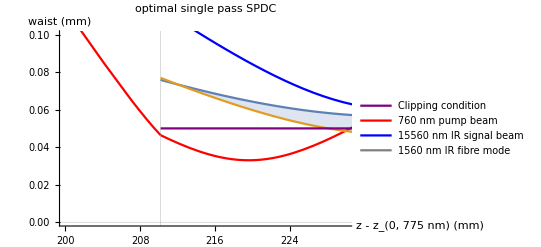

```mathematica
focusingplot[150,100.6,66.4,143.8,99,192.2,200,230,0,0.1]
```

Let’s play a little bit:

```mathematica
Manipulate[focusingplot[f1mm,f2mm,z1mm,z2mm,z4mm,z5mm,PlotRangeXmin,PlotRangeXmax,PlotRangeYmin,PlotRangeYmax],
{{f1mm,150},10,400},
{{f2mm,150},10,400},
{{z1mm,150},10,400},
{{z2mm,150},10,400},
{{z4mm,150},10,400},
{{z5mm,150},10,400},
{{PlotRangeXmin,0},0,400},
{{PlotRangeXmax,500},0,1500},
{{PlotRangeYmin,0},0,3},
{{PlotRangeYmax,2},0,3}
]
```

Ok, this seems to make sense:

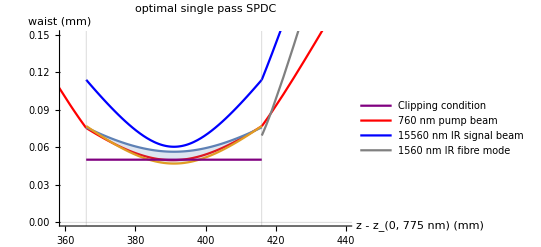

```mathematica
focusingplot[225,150,156.5,209.5,150,150,360,440,0,0.15]
```

(For a 5 cm crystal)

### Phase matching

We are pretty certain we will use PPLN for our crystals. The polling should be:

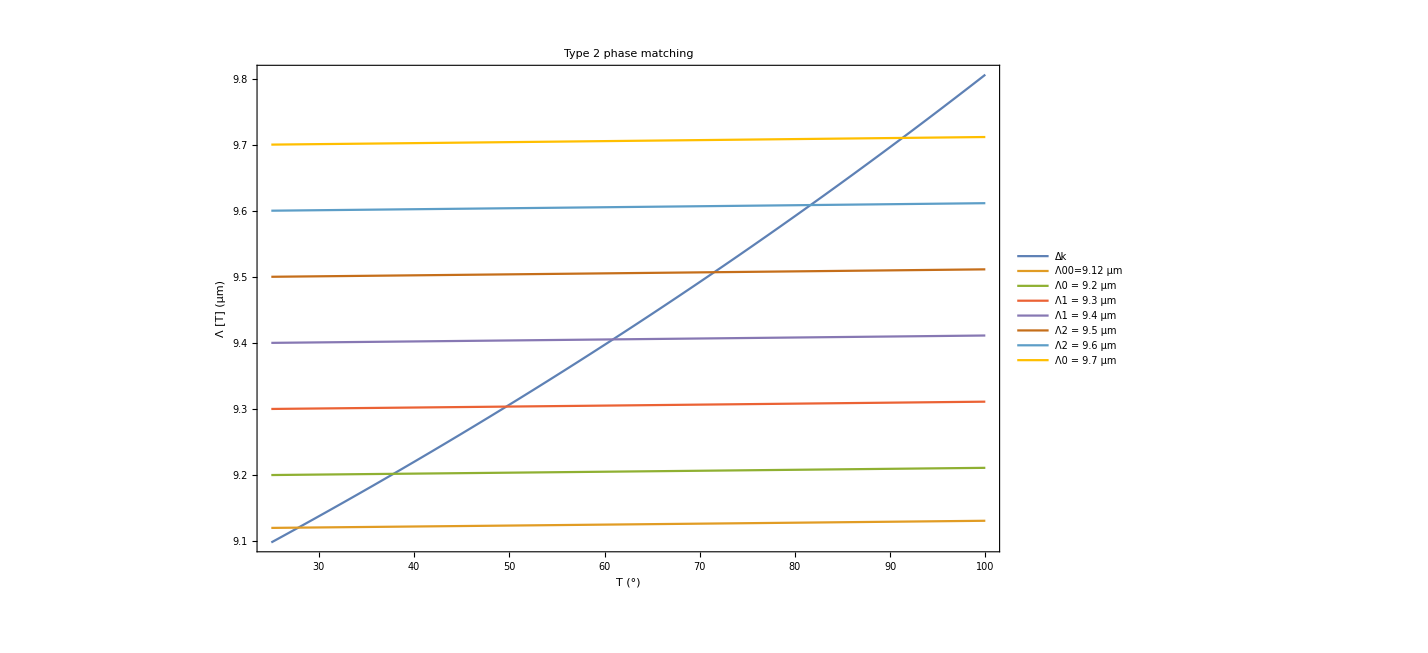

```mathematica
Module[{λp,λs,λi,T,Λ00,ΛT,Λ0,Λ1,Λ2,Λ3,Λ4,Λ5},
λp=780 10^-9;
λs=2λp;
λi=2λp;
Λ00=9.12;
Λ0=9.2;
Λ1=9.3;
Λ2=9.4;
Λ3=9.5;
Λ4=9.6;
Λ5=9.7;
Plot[{(n5oGayer[T,λp 10^6]/(λp 10^6)-n5eGayer[T,λs  10^6]/(λs 10^6)-n5oGayer[T,λi  10^6]/(λi 10^6))^-1,ΛtempLiNbO3[Λ00,T],ΛtempLiNbO3[Λ0,T],ΛtempLiNbO3[Λ1,T],ΛtempLiNbO3[Λ2,T],ΛtempLiNbO3[Λ3,T],ΛtempLiNbO3[Λ4,T],ΛtempLiNbO3[Λ5,T]},{T,25,100},Frame->True,Axes->None,PlotLabel->"Type 2 phase matching",PlotLegends->{"Δk","Λ00=9.12 μm","Λ0 = 9.2 μm","Λ1 = 9.3 μm","Λ1 = 9.4 μm","Λ2 = 9.5 μm","Λ2 = 9.6 μm","Λ0 = 9.7 μm"},
FrameLabel->{"T (°)","Λ [T] (μm)"},PlotRange->All]
]
```

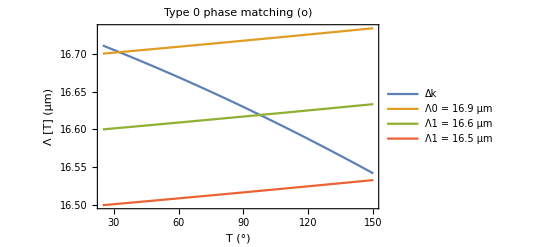

```mathematica
Module[{λp,λs,λi,T,ΛT,Λ0,Λ1,Λ2,Λ3,Λ4,Λ5},
λp=780 10^-9;
λs=2λp;
λi=2λp;
Λ0=16.7;
Λ1=16.6;
Λ2=16.5;
Plot[{(n5oGayer[T,λp 10^6]/(λp 10^6)-n5oGayer[T,λs  10^6]/(λs 10^6)-n5oGayer[T,λi  10^6]/(λi 10^6))^-1,ΛtempLiNbO3[Λ0,T],ΛtempLiNbO3[Λ1,T],ΛtempLiNbO3[Λ2,T],ΛtempLiNbO3[Λ3,T],ΛtempLiNbO3[Λ4,T],ΛtempLiNbO3[Λ5,T]},{T,25,150},Frame->True,Axes->None,PlotLabel->"Type 0 phase matching (o)",PlotLegends->{"Δk","Λ0 = 16.9 μm","Λ1 = 16.6 μm","Λ1 = 16.5 μm"},
FrameLabel->{"T (°)","Λ [T] (μm)"},PlotRange->All]
]
```

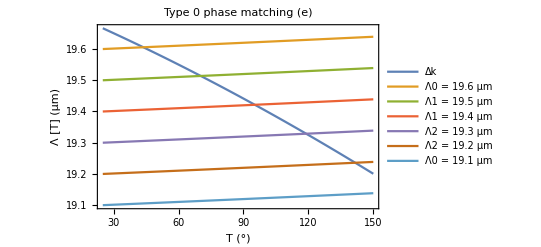

```mathematica
Module[{λp,λs,λi,T,ΛT,Λ0,Λ1,Λ2,Λ3,Λ4,Λ5},
λp=780 10^-9;
λs=2λp;
λi=2λp;
Λ0=19.6;
Λ1=19.5;
Λ2=19.4;
Λ3=19.3;
Λ4=19.2;
Λ5=19.1;
Plot[{(n5eGayer[T,λp 10^6]/(λp 10^6)-n5eGayer[T,λs  10^6]/(λs 10^6)-n5eGayer[T,λi  10^6]/(λi 10^6))^-1,ΛtempLiNbO3[Λ0,T],ΛtempLiNbO3[Λ1,T],ΛtempLiNbO3[Λ2,T],ΛtempLiNbO3[Λ3,T],ΛtempLiNbO3[Λ4,T],ΛtempLiNbO3[Λ5,T]},{T,25,150},Frame->True,Axes->None,PlotLabel->"Type 0 phase matching (e)",PlotLegends->{"Δk","Λ0 = 19.6 μm","Λ1 = 19.5 μm","Λ1 = 19.4 μm","Λ2 = 19.3 μm","Λ2 = 19.2 μm","Λ0 = 19.1 μm"},
FrameLabel->{"T (°)","Λ [T] (μm)"},PlotRange->All]
]
```

### bandwidth (type 2)

The SPDC bandwidth is determined from the phase mismatch of the nonlinear process. The most important factors (that we can control) here are the crystal lengths and the temperature:

Δk==((∂Δk)/(∂ω_s))_ω_p(ω_s-ω_(s,0)) +1/2 ((∂^2 Δk)/(∂ω_s^2))_ω_p(ω_s-ω_(s,0))^2 +((∂Δk)/(∂ω_p))_ω_s (ω_p-ω_(p,0)) +(∂Δk)/(∂T) (T-T_0)

Then our SPDC bandwidth is given by the FWHM of a sinc^2 function (the generated field goes with the sinc), so the SPDC bandwidth should be given by:

(sinc[Δk L/2])^2==1/2

In general, we have:

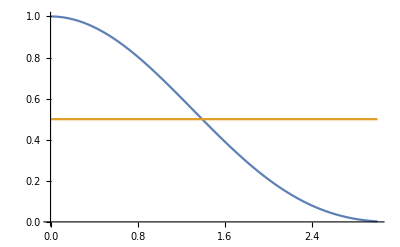

```mathematica
Plot[{(Sin[x]/x)^2,0.5},{x,0,3}]
```

```mathematica
FindRoot[(Sin[ξ]/ξ)^2==0.5,{ξ,1.5/π}]
```

{ξ→1.39156}

let us define that value as:

ξ==1.39156

Then the SPDC bandwidth should be:

(Δk L)/2==ξ

Δk==(2ξ)/L==((∂Δk)/(∂ω_s))_ω_p(ω_s-ω_(s,0))+1/2 ((∂^2 Δk)/(∂ω_s^2))_ω_p(ω_s-ω_(s,0))^2+((∂Δk)/(∂ω_p))_ω_s (ω_p-ω_(p,0))+(∂Δk)/(∂T) (T-T_0)+(∂Δk)/(∂V) V+Δk_0

So, in terms of the signal bandwidth, we should have:

((∂Δk)/(∂ω_s))_ω_p Δω_s+1/2 ((∂^2 Δk)/(∂ω_s^2))_ω_p Δω_s^2+Δk_0-(2 ξ)/L==0

WHAT is Δk_0? I would say that it is the phase mismatch we start from. If we start from perfect phase matching, then we should have Δk_0==0.

a quadratic equation we can write as:

a x^2+b x+c==0

with solutions:

(-b±√(b^2-4 a c))/(2a)

Δk[ωp_,ω1_,ω2_,T_,Λ_]

in order to get ν_FWHM we have to multiply this Δω_s by two:

Δν_FWHM = 1/(2π)2ω

This gives us:

```mathematica
ΔkGayer[ω1_,ω2_,T_,Λ_]:=Module[ {ωp,λp,λ1,λ2},
ωp=ω1+ω2;
λp= 2 π c/ωp;
λ1= 2 π c/ω1;
λ2= 2 π c/ω2;
2π(n5oGayer[T,λp 10^6]/λp-n5eGayer[T,λ1 10^6]/λ1-n5oGayer[T,λ2 10^6]/λ2-1/(ΛtempLiNbO3[Λ,T] 10^-6))
]
```

The SPDC bandwidth in the two crystals is defined as (note input requires phase matching temperature T0 and the maximum temperature offset T, for example for offset of 0.01 °: T - T0 = 0.01°):

```mathematica
SPDCbandwidthsignalGHzPlus[lc_,ω1_,ω2_,T_,TPM_,Λ_]:=Module[ {TC,Ca,Cb,Cc,ξ},
ξ=1.39155737825151;
Ca=1/2 Abs[Derivative[2,0,0,0][ΔkGayer][ω1,ω2,T,Λ]-Derivative[0,2,0,0][ΔkGayer][ω1,ω2,T,Λ]];
Cb=Abs[Derivative[1,0,0,0][ΔkGayer][ω1,ω2,T,Λ]-Derivative[0,1,0,0][ΔkGayer][ω1,ω2,T,Λ]];
Cc=-(2ξ)/ΛtempLiNbO3[2lc,T]+Derivative[0,0,1,0][ΔkGayer][ω1,ω2,T,Λ] (T-TPM);
2(-Cb+√(Cb^2-4 Ca Cc))/(2Ca)1/(2 π)10^-9 
]
```

```mathematica
SPDCbandwidthsignalGHzMinus[lc_,ω1_,ω2_,T_,TPM_,Λ_]:=Module[ {TC,Ca,Cb,Cc,ξ},
ξ=1.39155737825151;
Ca=1/2 Abs[Derivative[2,0,0,0][ΔkGayer][ω1,ω2,T,Λ]-Derivative[0,2,0,0][ΔkGayer][ω1,ω2,T,Λ]];
Cb=Abs[Derivative[1,0,0,0][ΔkGayer][ω1,ω2,T,Λ]-Derivative[0,1,0,0][ΔkGayer][ω1,ω2,T,Λ]];
Cc=-(2 ξ)/ΛtempLiNbO3[2lc,T]+Derivative[0,0,1,0][ΔkGayer][ω1,ω2,T,Λ] (T-TPM);
2(-Cb-√(Cb^2-4 Ca Cc))/(2Ca)1/(2 π)10^-9 
]
```

Let' s look at some numbers :

Gayer:

SPDC bandwidth, crystal 1, solution 1, in GHz: 33.0297

SPDC bandwidth, crystal 1, solution 2, in GHz: -1.30906×10^7

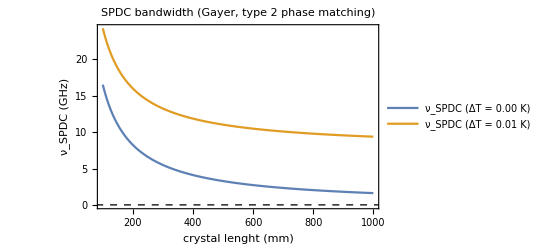

```mathematica
Module[{λp,λs,λi,T,TPM,ΛT,Λ0,ωp,ωs,ωi,lc,lcxmm,lcx,ΔT},
λp=780 10^-9;
ωp=(2 π c)/λp;
λs = 2λp;
λi = 2λp;
ωs=2 π c/λs;
ωi=2 π c/λi;
Λ0=9.4;
TPM=60.8;
T=TPM+ΔT;
lc=50 10^-3;
Print["Gayer:"];
Print["SPDC bandwidth, crystal 1, solution 1, in GHz: ",SPDCbandwidthsignalGHzPlus[lc,ωs,ωi,T,TPM,Λ0]/.{ΔT->0.00}];
Print["SPDC bandwidth, crystal 1, solution 2, in GHz: ",SPDCbandwidthsignalGHzMinus[lc,ωs,ωi,T,TPM,Λ0]/.{ΔT->0.00}];
Print[];

lcx=lcxmm 10^-3;

Plot[{SPDCbandwidthsignalGHzPlus[lcx,ωs,ωi,T,TPM,Λ0]/.{ΔT->0.00},SPDCbandwidthsignalGHzPlus[lcx,ωs,ωi,T,TPM,Λ0]/.{ΔT->0.01}},{lcxmm,100,1000},Frame->True,Axes->None,FrameLabel->{"crystal lenght (mm)","ν_SPDC (GHz)"},PlotLabel->Style["SPDC bandwidth (Gayer, type 2 phase matching)"],PlotStyle->{},PlotLegends->{"ν_SPDC (ΔT = 0.00 K)","ν_SPDC (ΔT = 0.01 K)"},GridLines->{{},{0,0.1}},GridLinesStyle->Directive[Black, Dashed]]
]
```

### bandwidth type 0

The SPDC bandwidth is determined from the phase mismatch of the nonlinear process. The most important factors (that we can control) here are the crystal lengths and the temperature:

Δk==((∂Δk)/(∂ω_s))_ω_p(ω_s-ω_(s,0)) +1/2 ((∂^2 Δk)/(∂ω_s^2))_ω_p(ω_s-ω_(s,0))^2 +((∂Δk)/(∂ω_p))_ω_s (ω_p-ω_(p,0)) +(∂Δk)/(∂T) (T-T_0)

Then our SPDC bandwidth is given by the FWHM of a sinc^2 function (the generated field goes with the sinc), so the SPDC bandwidth should be given by:

(sinc[Δk L/2])^2==1/2

In general, we have:

```mathematica
Plot[{(Sin[x]/x)^2,0.5},{x,0,3}]
```

-Graphics-

```mathematica
FindRoot[(Sin[ξ]/ξ)^2==0.5,{ξ,1.5/π}]
```

{ξ→1.39156}

let us define that value as:

ξ==1.39156

Then the SPDC bandwidth should be:

(Δk L)/2==ξ

Δk==(2ξ)/L==((∂Δk)/(∂ω_s))_ω_p(ω_s-ω_(s,0))+1/2 ((∂^2 Δk)/(∂ω_s^2))_ω_p(ω_s-ω_(s,0))^2+((∂Δk)/(∂ω_p))_ω_s (ω_p-ω_(p,0))+(∂Δk)/(∂T) (T-T_0)+(∂Δk)/(∂V) V+Δk_0

So, in terms of the signal bandwidth, we should have:

((∂Δk)/(∂ω_s))_ω_p Δω_s+1/2 ((∂^2 Δk)/(∂ω_s^2))_ω_p Δω_s^2+Δk_0-(2 ξ)/L==0

WHAT is Δk_0? I would say that it is the phase mismatch we start from. If we start from perfect phase matching, then we should have Δk_0==0.

a quadratic equation we can write as:

a x^2+b x+c==0

with solutions:

(-b±√(b^2-4 a c))/(2a)

Δk[ωp_,ω1_,ω2_,T_,Λ_]

in order to get ν_FWHM we have to multiply this Δω_s by two:

Δν_FWHM = 1/(2π)2ω

This gives us:

```mathematica
ΔkGayer[ω1_,ω2_,T_,Λ_]:=Module[ {ωp,λp,λ1,λ2},
ωp=ω1+ω2;
λp= 2 π c/ωp;
λ1= 2 π c/ω1;
λ2= 2 π c/ω2;
2π(n5oGayer[T,λp 10^6]/λp-n5oGayer[T,λ1 10^6]/λ1-n5oGayer[T,λ2 10^6]/λ2-1/(ΛtempLiNbO3[Λ,T] 10^-6))
]
```

The SPDC bandwidth in the two crystals is defined as (note input requires phase matching temperature T0 and the maximum temperature offset T, for example for offset of 0.01 °: T - T0 = 0.01°):

```mathematica
SPDCbandwidthsignalGHzPlus[lc_,ω1_,ω2_,T_,TPM_,Λ_]:=Module[ {TC,Ca,Cb,Cc,ξ},
ξ=1.39155737825151;
Ca=1/2 Abs[Derivative[2,0,0,0][ΔkGayer][ω1,ω2,T,Λ]-Derivative[0,2,0,0][ΔkGayer][ω1,ω2,T,Λ]];
Cb=Abs[Derivative[1,0,0,0][ΔkGayer][ω1,ω2,T,Λ]-Derivative[0,1,0,0][ΔkGayer][ω1,ω2,T,Λ]];
Cc=-(2ξ)/ΛtempLiNbO3[2lc,T]+Derivative[0,0,1,0][ΔkGayer][ω1,ω2,T,Λ] (T-TPM);
2(-Cb+√(Cb^2-4 Ca Cc))/(2Ca)1/(2 π)10^-9 
]
```

```mathematica
SPDCbandwidthsignalGHzMinus[lc_,ω1_,ω2_,T_,TPM_,Λ_]:=Module[ {TC,Ca,Cb,Cc,ξ},
ξ=1.39155737825151;
Ca=1/2 Abs[Derivative[2,0,0,0][ΔkGayer][ω1,ω2,T,Λ]-Derivative[0,2,0,0][ΔkGayer][ω1,ω2,T,Λ]];
Cb=Abs[Derivative[1,0,0,0][ΔkGayer][ω1,ω2,T,Λ]-Derivative[0,1,0,0][ΔkGayer][ω1,ω2,T,Λ]];
Cc=-(2 ξ)/ΛtempLiNbO3[2lc,T]+Derivative[0,0,1,0][ΔkGayer][ω1,ω2,T,Λ] (T-TPM);
2(-Cb-√(Cb^2-4 Ca Cc))/(2Ca)1/(2 π)10^-9 
]
```

Let' s look at some numbers :

Gayer:

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

SPDC bandwidth, crystal 1, solution 1, in GHz: Indeterminate

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

SPDC bandwidth, crystal 1, solution 2, in GHz: Indeterminate

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

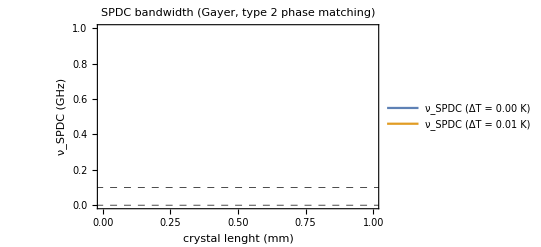

```mathematica
Module[{λp,λs,λi,T,TPM,ΛT,Λ0,ωp,ωs,ωi,lc,lcxmm,lcx,ΔT},
λp=780 10^-9;
ωp=(2 π c)/λp;
λs = 2λp;
λi = 2λp;
ωs=2 π c/λs;
ωi=2 π c/λi;
Λ0=16.6;
TPM=97.61;
T=TPM+ΔT;
lc=50 10^-3;
Print["Gayer:"];
Print["SPDC bandwidth, crystal 1, solution 1, in GHz: ",SPDCbandwidthsignalGHzPlus[lc,ωs,ωi,T,TPM,Λ0]/.{ΔT->0.00}];
Print["SPDC bandwidth, crystal 1, solution 2, in GHz: ",SPDCbandwidthsignalGHzMinus[lc,ωs,ωi,T,TPM,Λ0]/.{ΔT->0.00}];
Print[];

lcx=lcxmm 10^-3;

Plot[{SPDCbandwidthsignalGHzPlus[lcx,ωs,ωi,T,TPM,Λ0]/.{ΔT->0.00},SPDCbandwidthsignalGHzPlus[lcx,ωs,ωi,T,TPM,Λ0]/.{ΔT->0.01}},{lcxmm,100,1000},Frame->True,Axes->None,FrameLabel->{"crystal lenght (mm)","ν_SPDC (GHz)"},PlotLabel->Style["SPDC bandwidth (Gayer, type 2 phase matching)"],PlotStyle->{},PlotLegends->{"ν_SPDC (ΔT = 0.00 K)","ν_SPDC (ΔT = 0.01 K)"},GridLines->{{},{0,0.1}},GridLinesStyle->Directive[Black, Dashed]]
]
```